```mathematica
τ=1 (* τ *);
δ = 0;
τTrue = 27.2  10^-9;(* c *)
λ0 = 670.951 10^-9; (* м *)
cLight = 3 10^8 (* м/c *);
```

```mathematica
g = Range[1,8, 1];
e = Range[9, 24,1];
e = Delete[e, {{14-8}, {15-8}, {20-8}}]; (* при q=1 неактивны *)
```

## Print eq

```mathematica
ClearAll[Eq2Print];
Eq2Print[eq_] := eq /. {
ρ[β_, α_] :> Subscript["ρ", ToString[β]<>","<>ToString[α]],
ρRe[β_, α_] :> Subscript["ρ^re", ToString[β]<>","<>ToString[α]],
ρIm[β_, α_] :> "ρ^im"
};
```

## Научимся в C_(β α)

```mathematica
ClearAll[CRabi];
CRabi[{F2_, mF2_},{F1_, mF1_}, q_ : 1, 
Ι_ : 3/2, S_ : 1/2, J1_ : 1/2, J2_ : 3/2, L1_ : 0, L2_ : 1] := 
(-1)^(1/2 q(1+q) + 1 + 2 F1 - mF1 + Ι + J2 +S +L2 + J1)√((2 F1 + 1)(2 F2 + 1)(2 J1 +1)(2 J2 + 1)(2 L1 + 1)) ThreeJSymbol[{F1, -mF1},{1,q},{F2, mF2}] SixJSymbol[{J1,F1, Ι},{F2,J2,1}] SixJSymbol[{L1,J1,S},{J2,L2,1}] /; q + mF2 - mF1 == 0 && Abs[F1-F2] ≤ 1;
CRabi[{F2_, mF2_}, {F1_, mF1_}, q_ : 1, 
Ι_ : 3/2, S_ : 1/2, J1_ : 1/2, J2_ : 1/2, L1_ : 0, L2_ : 1] := 0;
```

```mathematica
ClearAll[objFmF];
objFmF = <|
1->{1, -1},2->{1,0},3->{1, 1} ,
4->{2, -2},5->{2, -1},6->{2, 0},7->{2, 1},8->{2, 2},
9->{3, -3},10->{3, -2},11->{3, -1},12->{3, 0},13->{3, 1},14->{3, 2},15->{3, 3},
16->{2, -2},17->{2, -1},18->{2, 0},19->{2, 1},20->{2, 2},
21->{1, -1},22->{1, 0},23->{1, 1},
24->{0, 0}
|>;
objωR = <|
1->0,2->0,3->0 ,
4->ω1,5->ω1,6->ω1,7->ω1,8->ω1,
9->0,10->0,11->0,12->0,13->0,14->0,15->0,
16->ω2,17->ω2,18->ω2,19->ω2,20->ω2,
21->ω3,22->ω3,23->ω3,
24->ω4
|>;
```

```mathematica
ClearAll[GetωR, GetCRabi,GetΩRabi];
GetωR[β_, α_] := ω0 + objωR[β] - objωR[α];
GetCRabi[β_, α_] :=CRabi[objFmF[β],objFmF[α]];
GetΩRabi[β_, α_, s_:1] :=20./τ √s GetCRabi[β, α];
```

## Добавим частоты

```mathematica
ω0 = 2 π cLight/λ0 τTrue;
ω1 = 803.5 10^6 τTrue;
ω2 = 9.2 10^6 τTrue;
ω3 = 6.2 10^6 τTrue;
ω4 = 3.1 10^6 τTrue;
```

```mathematica
(* тест *)
ω0- GetωR[24, 6]
N@GetCRabi[24, 3] 
GetΩRabi[24, 3]
```

21.7709

0.333333

6.66667

## Уравнение на эволюцию

```mathematica
ζ = 1;
```

```mathematica
(* чтобы сохранялись диагональные члены, ПОДГОН*)
ClearAll[SCALE];
SCALE[β_]:= Total@Map[GetCRabi[β,#]^2&, g];
```

```mathematica
Map[SCALE, e] // N
```

{0.333333,0.222222,0.133333,0.0666667,0.0222222,0.222222,0.166667,0.111111,0.0555556,0.144444,0.155556,0.0333333,0.111111}

```mathematica
ClearAll[GetGroundEvol, GetExitedEvol, GetReDiagonalEvol, GetImDiagonalEvol];
GetGroundEvol[α_] := 2ζ Total@Map[ρIm[#, α]GetΩRabi[#, α]&, e] + 1/τ Total@Map[ ρ[#, #]N@(GetCRabi[#, α]^2)&, e];
GetExitedEvol[β_] := -2 ζ Total@Map[ρIm[β, #]GetΩRabi[β, #]&, g] - 1/τ ρ[β, β]SCALE[β];
GetReDiagonalEvol[β_, α_] := (GetωR[β, α]-ω0 - δ)ρIm[β, α] -1/(2τ)ρRe[β, α]SCALE[β];
GetImDiagonalEvol[β_, α_] := ζ GetΩRabi[β, α](ρ[β, β] - ρ[α, α])-(GetωR[β, α]-ω0 - δ)ρRe[β, α] -1/(2τ)ρIm[β, α]SCALE[β];
```

```mathematica
(* тест *)
GetGroundEvol[2]// FullSimplify
GetExitedEvol[12] // FullSimplify
GetReDiagonalEvol[18, 3]// FullSimplify
GetImDiagonalEvol[18, 3] // FullSimplify
```

0.+0.0833333 ρ[17,17]+0.138889 ρ[21,21]+11.547 ρIm[17,2]+14.9071 ρIm[21,2]

0.-1/15 ρ[12,12]-10.328 ρIm[12,7]

0.25024 ρIm[18,3]-0.0555556 ρRe[18,3]

-3.33333 ρ[3,3]+3.33333 ρ[18,18]-0.0555556 ρIm[18,3]-0.25024 ρRe[18,3]

## Охапка переменных

```mathematica
ListρRe = Flatten@Outer[ρRe,e,g]; 
ListρIm = Flatten@Outer[ρIm,e,g]; 
Listρα = Map[ρ[#, #]&, g]; 
Listρβ = Map[ρ[#, #]&, e]; 
ListFull = Join[Listρα, Listρβ, ListρIm, ListρRe];
Tsubs = Map[# -> #[t]&,ListFull];
ListFullT = ListFull /. Tsubs;
Length@ListFull
```

229

```mathematica
varsI = ListFull;
varsII = Table[Unique[], {i, 1, Length[varsI], 1}];
subsI = Table[varsI[[i]]-> varsII[[i]], {i, 1, Length@varsI, 1}];
subsII = Table[varsII[[i]]-> varsI[[i]], {i, 1, Length@varsI, 1}];
```

```mathematica
(* занятный факт *)
Chop[FullSimplify[Total@Map[GetGroundEvol, g] + Total@Map[GetExitedEvol, e]]]
```

0

## Стационарная попытка

```mathematica
eqs = Join[
FullSimplify@Map[GetGroundEvol, g], 
FullSimplify@Map[GetExitedEvol, e], 
FullSimplify@Flatten@Outer[GetImDiagonalEvol,e,g] ,  
FullSimplify@Flatten@Outer[GetReDiagonalEvol,e,g] ];
```

```mathematica
eqsI = eqs;
eqsII = eqsI /. subsI;
```

```mathematica
coefs = Normal@CoefficientArrays[eqsII,varsII][[2]] ;
coefsSA = SparseArray[coefs];
arrIC = RandomReal[{0, 1}, 21];
arrIC = arrIC/ Total[arrIC];
IC = Join[arrIC, ConstantArray[0, Length@varsI-21]];
exp = MatrixExp[500 coefsSA];
g1 = Total[(exp.IC)[[ 1;;3]]];
g2 = Total[(exp.IC)[[ 4;;8]]];
e3 = Total[(exp.IC)[[ 9;;13]]];
e2 = Total[(exp.IC)[[ 14;;17]]];
e1 = Total[(exp.IC)[[ 18;;20]]];
e0 = Total[(exp.IC)[[ 21]]];
{g1, g2, e3, e2, e1, e0}
```

{0.0677978,0.723501,0.0719557,0.0722558,0.0463569,0.018133}

## Эволюция руками

```mathematica
arrIC = RandomReal[{0, 1}, 21];
arrIC = arrIC/ Total[arrIC];
IC = Join[arrIC, ConstantArray[0, Length@varsI-21]];
Total[(MatrixExp[100 coefsSA].IC)[[;;8]]]
```

0.910498

```mathematica
dt = 0.00001;
```

```mathematica
ClearAll[DoStep];
DoStep[state_] := state + dt coefsSA.state ;
DoNStep[state_] := Nest[DoStep, state, 2000]
```

```mathematica
IC = evol[[-1]];
evol = NestList[DoNStep, IC, 5000];
Total@evol[[-1]][[;;21]]
MinMax@evol[[-1]]
```

1.

{-0.000640651,0.301193}

```mathematica
Total[evol[[;;, 1;;3]], {2}][[-1]]
Total[evol[[;;, 4;;8]], {2}][[-1]]
Total[evol[[;;, 9;;13]], {2}][[-1]]
Total[evol[[;;, 14;;17]], {2}][[-1]]
Total[evol[[;;, 18;;20]], {2}][[-1]]
Total[evol[[;;,21]], {2}][[-1]]
```

0.023785

0.899142

0.0240171

0.0255705

0.0184705

0.00901468

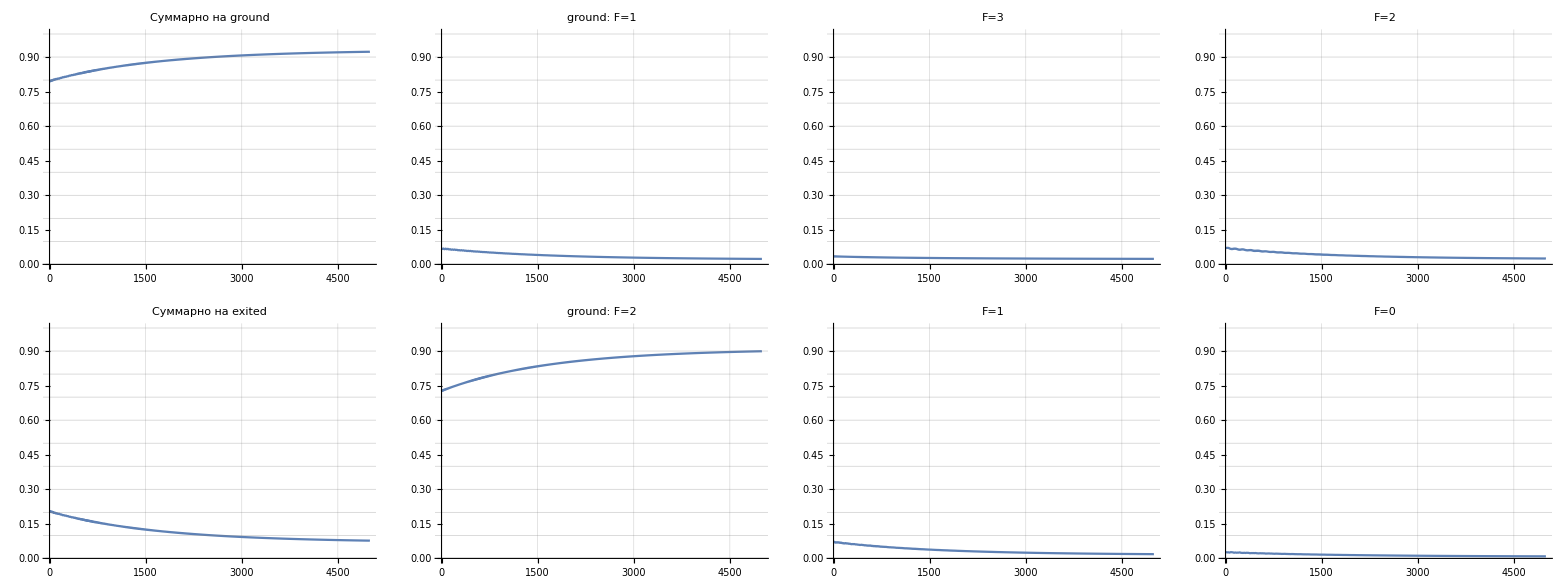

```mathematica
img1 = ListLinePlot[Total[evol[[;;, ;;8]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"Суммарно на ground"];
imgG1 = ListLinePlot[Total[evol[[;;, 1;;3]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"ground: F=1"];
imgG2 = ListLinePlot[Total[evol[[;;, 4;;8]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"ground: F=2"];
img0 = ListLinePlot[Total[evol[[;;, 9;;21]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"Суммарно на exited"];
img2 = ListLinePlot[Total[evol[[;;, 9;;13]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"F=3"];
img3 = ListLinePlot[Total[evol[[;;, 14;;17]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"F=2"];
img4 = ListLinePlot[Total[evol[[;;, 18;;20]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"F=1"];
img5  = ListLinePlot[Total[evol[[;;,21]], {2}], PlotRange->{Automatic,{0, 1}}, GridLines->{Automatic, Range[0, 1, 0.1]}, PlotLabel->"F=0"];
TableForm[{{img1, imgG1, img2, img3}, {img0, imgG2, img4, img5 }}]
```

```mathematica
coefsSA//ArrayPlot
```

-Graphics-

```mathematica
Total[(MatrixExp[coefsSA].IC)[[;;8]]]
```

0.799217

## Другое

```mathematica
tab = Table[Coefficient[eqs⟦i⟧, ListFull⟦j⟧], {i, 1, Length@eqs}, {j, 1, Length@ListFull}];
```

```mathematica
Dimensions@tab
MatrixRank@tab
Length@ListFull
```

{229,229}

224

229

```mathematica
(*Total[Join[Listρα,Listρβ] /. Chop[NSolve[tab.ListFull ==RandomReal[{-0.001, 0.001},Length@ListFull], ListFull, Reals], 10^-5]]*)
```

```mathematica
Chop[NSolve[tab.ListFull == ConstantArray[0, Length@ListFull] && (Total@Listρα + Total@Listρβ == 1), ListFull, Reals], 10^-5]
```

{{ρ[1,1]→0.226653 ρRe[16,5],ρ[2,2]→0.716476 ρRe[21,6],ρ[3,3]→0.0000145307,ρ[4,4]→0.99058-127.886 ρRe[16,5]-406.414 ρRe[21,6]-165.609 ρRe[23,8],ρ[5,5]→127.518 ρRe[16,5],ρ[6,6]→404.786 ρRe[21,6],ρ[7,7]→0.00829496,ρ[8,8]→165.245 ρRe[23,8],ρ[9,9]→0.00107336-0.138573 ρRe[16,5]-0.440378 ρRe[21,6]-0.17945 ρRe[23,8],ρ[10,10]→0.138175 ρRe[16,5],ρ[11,11]→0.438614 ρRe[21,6],ρ[12,12]→0,ρ[13,13]→0.179054 ρRe[23,8],ρ[16,16]→0.141389 ρRe[16,5],ρ[17,17]→0.447458 ρRe[21,6],ρ[18,18]→0,ρ[19,19]→0.183219 ρRe[23,8],ρ[21,21]→0.465833 ρRe[21,6],ρ[22,22]→0,ρ[23,23]→0.181845 ρRe[23,8],ρ[24,24]→0,ρIm[9,1]→0,ρIm[9,2]→0,ρIm[9,3]→0,ρIm[9,4]→-0.000430352+0.0555592 ρRe[16,5]+0.176564 ρRe[21,6]+0.0719481 ρRe[23,8],ρIm[9,5]→0,ρIm[9,6]→0,ρIm[9,7]→0,ρIm[9,8]→0,ρIm[10,1]→0,ρIm[10,2]→0,ρIm[10,3]→0,ρIm[10,4]→0,ρIm[10,5]→-0.0452335 ρRe[16,5],ρIm[10,6]→0,ρIm[10,7]→0,ρIm[10,8]→0,ρIm[11,1]→0,ρIm[11,2]→0,ρIm[11,3]→0,ρIm[11,4]→0,ρIm[11,5]→0,ρIm[11,6]→-0.111222 ρRe[21,6],ρIm[11,7]→0,ρIm[11,8]→0,ρIm[12,1]→0,ρIm[12,2]→0,ρIm[12,3]→0,ρIm[12,4]→0,ρIm[12,5]→0,ρIm[12,6]→0,ρIm[12,7]→0,ρIm[12,8]→0,ρIm[13,1]→0,ρIm[13,2]→0,ρIm[13,3]→0,ρIm[13,4]→0,ρIm[13,5]→0,ρIm[13,6]→0,ρIm[13,7]→0,ρIm[13,8]→-0.018536 ρRe[23,8],ρIm[16,1]→-0.0400846 ρRe[16,5],ρIm[16,2]→0,ρIm[16,3]→0,ρIm[16,4]→0,ρIm[16,5]→-0.0231428 ρRe[16,5],ρIm[16,6]→0,ρIm[16,7]→0,ρIm[16,8]→0,ρIm[17,1]→0,ρIm[17,2]→-0.0894287 ρRe[21,6],ρIm[17,3]→0,ρIm[17,4]→0,ρIm[17,5]→0,ρIm[17,6]→-0.0899741 ρRe[21,6],ρIm[17,7]→0,ρIm[17,8]→0,ρIm[18,1]→0,ρIm[18,2]→0,ρIm[18,3]→0,ρIm[18,4]→0,ρIm[18,5]→0,ρIm[18,6]→0,ρIm[18,7]→0,ρIm[18,8]→0,ρIm[19,1]→0,ρIm[19,2]→0,ρIm[19,3]→0,ρIm[19,4]→0,ρIm[19,5]→0,ρIm[19,6]→0,ρIm[19,7]→0,ρIm[19,8]→-0.0299897 ρRe[23,8],ρIm[21,1]→0,ρIm[21,2]→-0.120771 ρRe[21,6],ρIm[21,3]→0,ρIm[21,4]→0,ρIm[21,5]→0,ρIm[21,6]→-0.0230558 ρRe[21,6],ρIm[21,7]→0,ρIm[21,8]→0,ρIm[22,1]→0,ρIm[22,2]→0,ρIm[22,3]→0,ρIm[22,4]→0,ρIm[22,5]→0,ρIm[22,6]→0,ρIm[22,7]→0,ρIm[22,8]→0,ρIm[23,1]→0,ρIm[23,2]→0,ρIm[23,3]→0,ρIm[23,4]→0,ρIm[23,5]→0,ρIm[23,6]→0,ρIm[23,7]→0,ρIm[23,8]→-0.0230558 ρRe[23,8],ρIm[24,1]→0,ρIm[24,2]→0,ρIm[24,3]→0,ρIm[24,4]→0,ρIm[24,5]→0,ρIm[24,6]→0,ρIm[24,7]→0,ρIm[24,8]→0,ρRe[9,1]→0,ρRe[9,2]→0,ρRe[9,3]→0,ρRe[9,4]→0.0188109-2.42852 ρRe[16,5]-7.71769 ρRe[21,6]-3.14488 ρRe[23,8],ρRe[9,5]→0,ρRe[9,6]→0,ρRe[9,7]→0,ρRe[9,8]→0,ρRe[10,1]→0,ρRe[10,2]→0,ρRe[10,3]→0,ρRe[10,4]→0,ρRe[10,5]→1.97717 ρRe[16,5],ρRe[10,6]→0,ρRe[10,7]→0,ρRe[10,8]→0,ρRe[11,1]→0,ρRe[11,2]→0,ρRe[11,3]→0,ρRe[11,4]→0,ρRe[11,5]→0,ρRe[11,6]→4.86154 ρRe[21,6],ρRe[11,7]→0,ρRe[11,8]→0,ρRe[12,1]→0,ρRe[12,2]→0,ρRe[12,3]→0,ρRe[12,4]→0,ρRe[12,5]→0,ρRe[12,6]→0,ρRe[12,7]→0.0000704447,ρRe[12,8]→0,ρRe[13,1]→0,ρRe[13,2]→0,ρRe[13,3]→0,ρRe[13,4]→0,ρRe[13,5]→0,ρRe[13,6]→0,ρRe[13,7]→0,ρRe[13,8]→0.810217 ρRe[23,8],ρRe[16,1]→-0.0200615 ρRe[16,5],ρRe[16,2]→0,ρRe[16,3]→0,ρRe[16,4]→0,ρRe[16,6]→0,ρRe[16,7]→0,ρRe[16,8]→0,ρRe[17,1]→0,ρRe[17,2]→-0.0447573 ρRe[21,6],ρRe[17,3]→0,ρRe[17,4]→0,ρRe[17,5]→0,ρRe[17,6]→3.88777 ρRe[21,6],ρRe[17,7]→0,ρRe[17,8]→0,ρRe[18,1]→0,ρRe[18,2]→0,ρRe[18,3]→0,ρRe[18,4]→0,ρRe[18,5]→0,ρRe[18,6]→0,ρRe[18,7]→0.0000796694,ρRe[18,8]→0,ρRe[19,1]→0,ρRe[19,2]→0,ρRe[19,3]→0,ρRe[19,4]→0,ρRe[19,5]→0,ρRe[19,6]→0,ρRe[19,7]→0,ρRe[19,8]→1.29585 ρRe[23,8],ρRe[21,1]→0,ρRe[21,2]→-0.0407335 ρRe[21,6],ρRe[21,3]→0,ρRe[21,4]→0,ρRe[21,5]→0,ρRe[21,7]→0,ρRe[21,8]→0,ρRe[22,1]→0,ρRe[22,2]→0,ρRe[22,3]→0,ρRe[22,4]→0,ρRe[22,5]→0,ρRe[22,6]→0,ρRe[22,7]→0.000035494,ρRe[22,8]→0,ρRe[23,1]→0,ρRe[23,2]→0,ρRe[23,3]→0,ρRe[23,4]→0,ρRe[23,5]→0,ρRe[23,6]→0,ρRe[23,7]→0,ρRe[24,1]→0,ρRe[24,2]→0,ρRe[24,3]→0,ρRe[24,4]→0,ρRe[24,5]→0,ρRe[24,6]→0,ρRe[24,7]→0,ρRe[24,8]→0}}

## Нестационарная попытка

```mathematica
EQS = Join[
FullSimplify@Map[(GetGroundEvol[#]/.Tsubs)== D[ρ[#,#][t], t]&, g],
FullSimplify@Map[(GetExitedEvol[#]/.Tsubs)== D[ρ[#,#][t], t]&, e],
FullSimplify@Flatten@Outer[(N@GetImDiagonalEvol[#1, #2]/.Tsubs) ==  D[ρ[#1,#2][t], t]&,e,g] ,
FullSimplify@Flatten@Outer[(N@GetReDiagonalEvol[#1, #2]/.Tsubs)  ==  D[ρ[#1,#2][t], t]&,e,g] 
];
Length@EQS
```

229

```mathematica
IC = Join[Map[#[0] == 0.125&, Listρα], Map[#[0] == 0.&, Listρβ], Map[#[0] == 0&, ListρRe], Map[#[0] == 0&, ListρIm]];
Length@IC
```

229

```mathematica
FullEQS = Join[EQS, IC];
tMax =1;
NDSolve[FullEQS, ListFull, {t, 0, tMax}]
```

NDSolve::overdet: There are fewer dependent variables, {ρ[1,1][t],ρ[2,2][t],ρ[3,3][t],ρ[4,4][t],ρ[5,5][t],ρ[6,6][t],ρ[7,7][t],ρ[8,8][t],ρ[9,1][t],ρ[9,2][t],«133»}, than equations, so the system is overdetermined.

NDSolve[{0.+0.166667 ρ[16,16][t]+0.194 ρIm[16,1][t]==ρ[1,1]'[t],0.+0.0833333 ρ[17,17][t]+0.138889 ρ[21,21][t]+0.137178 ρIm[17,2][t]+0.177097 ρIm[21,2][t]==ρ[2,2]'[t],0.+0.0277778 ρ[18,18][t]+0.138889 ρ[22,22][t]+0.111111 ρ[24,24][t]+0.0792 ρIm[18,3][t]+0.177097 ρIm[22,3][t]+0.1584 ρIm[24,3][t]==ρ[3,3]'[t],0.+0.333333 ρ[9,9][t]+0.274357 ρIm[9,4][t]==ρ[4,4]'[t],0.+0.222222 ρ[10,10][t]+0.0555556 ρ[16,16][t]+0.224011 ρIm[10,5][t]+0.112006 ρIm[16,5][t]==ρ[5,5]'[t],0.+0.133333 ρ[11,11][t]+0.0833333 ρ[17,17][t]+0.00555556 ρ[21,21][t]+0.173519 ρIm[11,6][t]+0.137178 ρIm[17,6][t]+0.0354193 ρIm[21,6][t]==ρ[6,6]'[t],0.+0.0666667 ρ[12,12][t]+0.0833333 ρ[18,18][t]+0.0166667 ρ[22,22][t]+0.122696 ρIm[12,7][t]+0.137178 ρIm[18,7][t]+0.0613481 ρIm[22,7][t]==ρ[7,7]'[t],0.+0.0222222 ρ[13,13][t]+0.0555556 ρ[19,19][t]+0.0333333 ρ[23,23][t]+0.0708386 ρIm[13,8][t]+0.112006 ρIm[19,8][t]+0.0867593 ρIm[23,8][t]==ρ[8,8]'[t],1/3 ρ[9,9][t]+0.274357 ρIm[9,4][t]+ρ[9,9]'[t]==0.,2/9 ρ[10,10][t]+0.224011 ρIm[10,5][t]+ρ[10,10]'[t]==0.,1. ρ[11,11][t]+1.30139 ρIm[11,6][t]+7.5 ρ[11,11]'[t]==0,1. ρ[12,12][t]+1.84044 ρIm[12,7][t]+15. ρ[12,12]'[t]==0,1. ρ[13,13][t]+3.18774 ρIm[13,8][t]+45. ρ[13,13]'[t]==0,2/9 ρ[16,16][t]+0.194 ρIm[16,1][t]+0.112006 ρIm[16,5][t]+ρ[16,16]'[t]==0.,1/6 ρ[17,17][t]+0.137178 ρIm[17,2][t]+0.137178 ρIm[17,6][t]+ρ[17,17]'[t]==0.,1/9 ρ[18,18][t]+0.0792 ρIm[18,3][t]+0.137178 ρIm[18,7][t]+ρ[18,18]'[t]==0.,1. ρ[19,19][t]+2.0161 ρIm[19,8][t]+18. ρ[19,19]'[t]==0,1. ρ[21,21][t]+1.22605 ρIm[21,2][t]+0.245211 ρIm[21,6][t]+6.92308 ρ[21,21]'[t]==0,1. ρ[22,22][t]+1.13848 ρIm[22,3][t]+0.39438 ρIm[22,7][t]+6.42857 ρ[22,22]'[t]==0,1. ρ[23,23][t]+2.60278 ρIm[23,8][t]+30. ρ[23,23]'[t]==0,1/9 ρ[24,24][t]+0.1584 ρIm[24,3][t]+ρ[24,24]'[t]==0.,0.-0.166667 ρIm[9.,1.]==ρ[9,1]'[t],0.-0.166667 ρIm[9.,2.]==ρ[9,2]'[t],0.-0.166667 ρIm[9.,3.]==ρ[9,3]'[t],-0.137178 ρ[4.,4.]+0.137178 ρ[9.,9.]-0.166667 ρIm[9.,4.]+21.8552 ρRe[9.,4.]==ρ[9,4]'[t],0.-0.166667 ρIm[9.,5.]+21.8552 ρRe[9.,5.]==ρ[9,5]'[t],0.-0.166667 ρIm[9.,6.]+21.8552 ρRe[9.,6.]==ρ[9,6]'[t],0.-0.166667 ρIm[9.,7.]+21.8552 ρRe[9.,7.]==ρ[9,7]'[t],0.-0.166667 ρIm[9.,8.]+21.8552 ρRe[9.,8.]==ρ[9,8]'[t],0.-0.111111 ρIm[10.,1.]==ρ[10,1]'[t],0.-0.111111 ρIm[10.,2.]==ρ[10,2]'[t],0.-0.111111 ρIm[10.,3.]==ρ[10,3]'[t],0.-0.111111 ρIm[10.,4.]+21.8552 ρRe[10.,4.]==ρ[10,4]'[t],-0.112006 ρ[5.,5.]+0.112006 ρ[10.,10.]-0.111111 ρIm[10.,5.]+21.8552 ρRe[10.,5.]==ρ[10,5]'[t],0.-0.111111 ρIm[10.,6.]+21.8552 ρRe[10.,6.]==ρ[10,6]'[t],0.-0.111111 ρIm[10.,7.]+21.8552 ρRe[10.,7.]==ρ[10,7]'[t],0.-0.111111 ρIm[10.,8.]+21.8552 ρRe[10.,8.]==ρ[10,8]'[t],0.-0.0666667 ρIm[11.,1.]==ρ[11,1]'[t],0.-0.0666667 ρIm[11.,2.]==ρ[11,2]'[t],0.-0.0666667 ρIm[11.,3.]==ρ[11,3]'[t],0.-0.0666667 ρIm[11.,4.]+21.8552 ρRe[11.,4.]==ρ[11,4]'[t],0.-0.0666667 ρIm[11.,5.]+21.8552 ρRe[11.,5.]==ρ[11,5]'[t],-0.0867593 ρ[6.,6.]+0.0867593 ρ[11.,11.]-0.0666667 ρIm[11.,6.]+21.8552 ρRe[11.,6.]==ρ[11,6]'[t],0.-0.0666667 ρIm[11.,7.]+21.8552 ρRe[11.,7.]==ρ[11,7]'[t],0.-0.0666667 ρIm[11.,8.]+21.8552 ρRe[11.,8.]==ρ[11,8]'[t],0.-0.0333333 ρIm[12.,1.]==ρ[12,1]'[t],0.-0.0333333 ρIm[12.,2.]==ρ[12,2]'[t],0.-0.0333333 ρIm[12.,3.]==ρ[12,3]'[t],0.-0.0333333 ρIm[12.,4.]+21.8552 ρRe[12.,4.]==ρ[12,4]'[t],0.-0.0333333 ρIm[12.,5.]+21.8552 ρRe[12.,5.]==ρ[12,5]'[t],0.-0.0333333 ρIm[12.,6.]+21.8552 ρRe[12.,6.]==ρ[12,6]'[t],-0.0613481 ρ[7.,7.]+0.0613481 ρ[12.,12.]-0.0333333 ρIm[12.,7.]+21.8552 ρRe[12.,7.]==ρ[12,7]'[t],0.-0.0333333 ρIm[12.,8.]+21.8552 ρRe[12.,8.]==ρ[12,8]'[t],0.-0.0111111 ρIm[13.,1.]==ρ[13,1]'[t],0.-0.0111111 ρIm[13.,2.]==ρ[13,2]'[t],0.-0.0111111 ρIm[13.,3.]==ρ[13,3]'[t],0.-0.0111111 ρIm[13.,4.]+21.8552 ρRe[13.,4.]==ρ[13,4]'[t],0.-0.0111111 ρIm[13.,5.]+21.8552 ρRe[13.,5.]==ρ[13,5]'[t],0.-0.0111111 ρIm[13.,6.]+21.8552 ρRe[13.,6.]==ρ[13,6]'[t],0.-0.0111111 ρIm[13.,7.]+21.8552 ρRe[13.,7.]==ρ[13,7]'[t],-0.0354193 ρ[8.,8.]+0.0354193 ρ[13.,13.]-0.0111111 ρIm[13.,8.]+21.8552 ρRe[13.,8.]==ρ[13,8]'[t],-0.0969998 ρ[1.,1.]+0.0969998 ρ[16.,16.]-0.111111 ρIm[16.,1.]-0.25024 ρRe[16.,1.]==ρ[16,1]'[t],0.-0.111111 ρIm[16.,2.]-0.25024 ρRe[16.,2.]==ρ[16,2]'[t],0.-0.111111 ρIm[16.,3.]-0.25024 ρRe[16.,3.]==ρ[16,3]'[t],0.-0.111111 ρIm[16.,4.]+21.605 ρRe[16.,4.]==ρ[16,4]'[t],-0.0560029 ρ[5.,5.]+0.0560029 ρ[16.,16.]-0.111111 ρIm[16.,5.]+21.605 ρRe[16.,5.]==ρ[16,5]'[t],0.-0.111111 ρIm[16.,6.]+21.605 ρRe[16.,6.]==ρ[16,6]'[t],0.-0.111111 ρIm[16.,7.]+21.605 ρRe[16.,7.]==ρ[16,7]'[t],0.-0.111111 ρIm[16.,8.]+21.605 ρRe[16.,8.]==ρ[16,8]'[t],0.-0.0833333 ρIm[17.,1.]-0.25024 ρRe[17.,1.]==ρ[17,1]'[t],-0.0685892 ρ[2.,2.]+0.0685892 ρ[17.,17.]-0.0833333 ρIm[17.,2.]-0.25024 ρRe[17.,2.]==ρ[17,2]'[t],0.-0.0833333 ρIm[17.,3.]-0.25024 ρRe[17.,3.]==ρ[17,3]'[t],0.-0.0833333 ρIm[17.,4.]+21.605 ρRe[17.,4.]==ρ[17,4]'[t],0.-0.0833333 ρIm[17.,5.]+21.605 ρRe[17.,5.]==ρ[17,5]'[t],-0.0685892 ρ[6.,6.]+0.0685892 ρ[17.,17.]-0.0833333 ρIm[17.,6.]+21.605 ρRe[17.,6.]==ρ[17,6]'[t],0.-0.0833333 ρIm[17.,7.]+21.605 ρRe[17.,7.]==ρ[17,7]'[t],0.-0.0833333 ρIm[17.,8.]+21.605 ρRe[17.,8.]==ρ[17,8]'[t],0.-0.0555556 ρIm[18.,1.]-0.25024 ρRe[18.,1.]==ρ[18,1]'[t],0.-0.0555556 ρIm[18.,2.]-0.25024 ρRe[18.,2.]==ρ[18,2]'[t],-0.0396 ρ[3.,3.]+0.0396 ρ[18.,18.]-0.0555556 ρIm[18.,3.]-0.25024 ρRe[18.,3.]==ρ[18,3]'[t],0.-0.0555556 ρIm[18.,4.]+21.605 ρRe[18.,4.]==ρ[18,4]'[t],0.-0.0555556 ρIm[18.,5.]+21.605 ρRe[18.,5.]==ρ[18,5]'[t],0.-0.0555556 ρIm[18.,6.]+21.605 ρRe[18.,6.]==ρ[18,6]'[t],-0.0685892 ρ[7.,7.]+0.0685892 ρ[18.,18.]-0.0555556 ρIm[18.,7.]+21.605 ρRe[18.,7.]==ρ[18,7]'[t],0.-0.0555556 ρIm[18.,8.]+21.605 ρRe[18.,8.]==ρ[18,8]'[t],0.-0.0277778 ρIm[19.,1.]-0.25024 ρRe[19.,1.]==ρ[19,1]'[t],0.-0.0277778 ρIm[19.,2.]-0.25024 ρRe[19.,2.]==ρ[19,2]'[t],0.-0.0277778 ρIm[19.,3.]-0.25024 ρRe[19.,3.]==ρ[19,3]'[t],0.-0.0277778 ρIm[19.,4.]+21.605 ρRe[19.,4.]==ρ[19,4]'[t],0.-0.0277778 ρIm[19.,5.]+21.605 ρRe[19.,5.]==ρ[19,5]'[t],0.-0.0277778 ρIm[19.,6.]+21.605 ρRe[19.,6.]==ρ[19,6]'[t],0.-0.0277778 ρIm[19.,7.]+21.605 ρRe[19.,7.]==ρ[19,7]'[t],-0.0560029 ρ[8.,8.]+0.0560029 ρ[19.,19.]-0.0277778 ρIm[19.,8.]+21.605 ρRe[19.,8.]==ρ[19,8]'[t],0.-0.0722222 ρIm[21.,1.]-0.16864 ρRe[21.,1.]==ρ[21,1]'[t],-0.0885483 ρ[2.,2.]+0.0885483 ρ[21.,21.]-0.0722222 ρIm[21.,2.]-0.16864 ρRe[21.,2.]==ρ[21,2]'[t],0.-0.0722222 ρIm[21.,3.]-0.16864 ρRe[21.,3.]==ρ[21,3]'[t],0.-0.0722222 ρIm[21.,4.]+21.6866 ρRe[21.,4.]==ρ[21,4]'[t],0.-0.0722222 ρIm[21.,5.]+21.6866 ρRe[21.,5.]==ρ[21,5]'[t],-0.0177097 ρ[6.,6.]+0.0177097 ρ[21.,21.]-0.0722222 ρIm[21.,6.]+21.6866 ρRe[21.,6.]==ρ[21,6]'[t],0.-0.0722222 ρIm[21.,7.]+21.6866 ρRe[21.,7.]==ρ[21,7]'[t],0.-0.0722222 ρIm[21.,8.]+21.6866 ρRe[21.,8.]==ρ[21,8]'[t],0.-0.0777778 ρIm[22.,1.]-0.16864 ρRe[22.,1.]==ρ[22,1]'[t],0.-0.0777778 ρIm[22.,2.]-0.16864 ρRe[22.,2.]==ρ[22,2]'[t],-0.0885483 ρ[3.,3.]+0.0885483 ρ[22.,22.]-0.0777778 ρIm[22.,3.]-0.16864 ρRe[22.,3.]==ρ[22,3]'[t],0.-0.0777778 ρIm[22.,4.]+21.6866 ρRe[22.,4.]==ρ[22,4]'[t],0.-0.0777778 ρIm[22.,5.]+21.6866 ρRe[22.,5.]==ρ[22,5]'[t],0.-0.0777778 ρIm[22.,6.]+21.6866 ρRe[22.,6.]==ρ[22,6]'[t],-0.030674 ρ[7.,7.]+0.030674 ρ[22.,22.]-0.0777778 ρIm[22.,7.]+21.6866 ρRe[22.,7.]==ρ[22,7]'[t],0.-0.0777778 ρIm[22.,8.]+21.6866 ρRe[22.,8.]==ρ[22,8]'[t],0.-0.0166667 ρIm[23.,1.]-0.16864 ρRe[23.,1.]==ρ[23,1]'[t],0.-0.0166667 ρIm[23.,2.]-0.16864 ρRe[23.,2.]==ρ[23,2]'[t],0.-0.0166667 ρIm[23.,3.]-0.16864 ρRe[23.,3.]==ρ[23,3]'[t],0.-0.0166667 ρIm[23.,4.]+21.6866 ρRe[23.,4.]==ρ[23,4]'[t],0.-0.0166667 ρIm[23.,5.]+21.6866 ρRe[23.,5.]==ρ[23,5]'[t],0.-0.0166667 ρIm[23.,6.]+21.6866 ρRe[23.,6.]==ρ[23,6]'[t],0.-0.0166667 ρIm[23.,7.]+21.6866 ρRe[23.,7.]==ρ[23,7]'[t],-0.0433796 ρ[8.,8.]+0.0433796 ρ[23.,23.]-0.0166667 ρIm[23.,8.]+21.6866 ρRe[23.,8.]==ρ[23,8]'[t],0.-0.0555556 ρIm[24.,1.]-0.08432 ρRe[24.,1.]==ρ[24,1]'[t],0.-0.0555556 ρIm[24.,2.]-0.08432 ρRe[24.,2.]==ρ[24,2]'[t],-0.0792 ρ[3.,3.]+0.0792 ρ[24.,24.]-0.0555556 ρIm[24.,3.]-0.08432 ρRe[24.,3.]==ρ[24,3]'[t],0.-0.0555556 ρIm[24.,4.]+21.7709 ρRe[24.,4.]==ρ[24,4]'[t],0.-0.0555556 ρIm[24.,5.]+21.7709 ρRe[24.,5.]==ρ[24,5]'[t],0.-0.0555556 ρIm[24.,6.]+21.7709 ρRe[24.,6.]==ρ[24,6]'[t],0.-0.0555556 ρIm[24.,7.]+21.7709 ρRe[24.,7.]==ρ[24,7]'[t],0.-0.0555556 ρIm[24.,8.]+21.7709 ρRe[24.,8.]==ρ[24,8]'[t],0.-0.166667 ρRe[9.,1.]==ρ[9,1]'[t],0.-0.166667 ρRe[9.,2.]==ρ[9,2]'[t],0.-0.166667 ρRe[9.,3.]==ρ[9,3]'[t],-21.8552 ρIm[9.,4.]-0.166667 ρRe[9.,4.]==ρ[9,4]'[t],-21.8552 ρIm[9.,5.]-0.166667 ρRe[9.,5.]==ρ[9,5]'[t],-21.8552 ρIm[9.,6.]-0.166667 ρRe[9.,6.]==ρ[9,6]'[t],-21.8552 ρIm[9.,7.]-0.166667 ρRe[9.,7.]==ρ[9,7]'[t],-21.8552 ρIm[9.,8.]-0.166667 ρRe[9.,8.]==ρ[9,8]'[t],0.-0.111111 ρRe[10.,1.]==ρ[10,1]'[t],0.-0.111111 ρRe[10.,2.]==ρ[10,2]'[t],0.-0.111111 ρRe[10.,3.]==ρ[10,3]'[t],-21.8552 ρIm[10.,4.]-0.111111 ρRe[10.,4.]==ρ[10,4]'[t],-21.8552 ρIm[10.,5.]-0.111111 ρRe[10.,5.]==ρ[10,5]'[t],-21.8552 ρIm[10.,6.]-0.111111 ρRe[10.,6.]==ρ[10,6]'[t],-21.8552 ρIm[10.,7.]-0.111111 ρRe[10.,7.]==ρ[10,7]'[t],-21.8552 ρIm[10.,8.]-0.111111 ρRe[10.,8.]==ρ[10,8]'[t],0.-0.0666667 ρRe[11.,1.]==ρ[11,1]'[t],0.-0.0666667 ρRe[11.,2.]==ρ[11,2]'[t],0.-0.0666667 ρRe[11.,3.]==ρ[11,3]'[t],-21.8552 ρIm[11.,4.]-0.0666667 ρRe[11.,4.]==ρ[11,4]'[t],-21.8552 ρIm[11.,5.]-0.0666667 ρRe[11.,5.]==ρ[11,5]'[t],-21.8552 ρIm[11.,6.]-0.0666667 ρRe[11.,6.]==ρ[11,6]'[t],-21.8552 ρIm[11.,7.]-0.0666667 ρRe[11.,7.]==ρ[11,7]'[t],-21.8552 ρIm[11.,8.]-0.0666667 ρRe[11.,8.]==ρ[11,8]'[t],0.-0.0333333 ρRe[12.,1.]==ρ[12,1]'[t],0.-0.0333333 ρRe[12.,2.]==ρ[12,2]'[t],0.-0.0333333 ρRe[12.,3.]==ρ[12,3]'[t],-21.8552 ρIm[12.,4.]-0.0333333 ρRe[12.,4.]==ρ[12,4]'[t],-21.8552 ρIm[12.,5.]-0.0333333 ρRe[12.,5.]==ρ[12,5]'[t],-21.8552 ρIm[12.,6.]-0.0333333 ρRe[12.,6.]==ρ[12,6]'[t],-21.8552 ρIm[12.,7.]-0.0333333 ρRe[12.,7.]==ρ[12,7]'[t],-21.8552 ρIm[12.,8.]-0.0333333 ρRe[12.,8.]==ρ[12,8]'[t],0.-0.0111111 ρRe[13.,1.]==ρ[13,1]'[t],0.-0.0111111 ρRe[13.,2.]==ρ[13,2]'[t],0.-0.0111111 ρRe[13.,3.]==ρ[13,3]'[t],-21.8552 ρIm[13.,4.]-0.0111111 ρRe[13.,4.]==ρ[13,4]'[t],-21.8552 ρIm[13.,5.]-0.0111111 ρRe[13.,5.]==ρ[13,5]'[t],-21.8552 ρIm[13.,6.]-0.0111111 ρRe[13.,6.]==ρ[13,6]'[t],-21.8552 ρIm[13.,7.]-0.0111111 ρRe[13.,7.]==ρ[13,7]'[t],-21.8552 ρIm[13.,8.]-0.0111111 ρRe[13.,8.]==ρ[13,8]'[t],0.25024 ρIm[16.,1.]-0.111111 ρRe[16.,1.]==ρ[16,1]'[t],0.25024 ρIm[16.,2.]-0.111111 ρRe[16.,2.]==ρ[16,2]'[t],0.25024 ρIm[16.,3.]-0.111111 ρRe[16.,3.]==ρ[16,3]'[t],-21.605 ρIm[16.,4.]-0.111111 ρRe[16.,4.]==ρ[16,4]'[t],-21.605 ρIm[16.,5.]-0.111111 ρRe[16.,5.]==ρ[16,5]'[t],-21.605 ρIm[16.,6.]-0.111111 ρRe[16.,6.]==ρ[16,6]'[t],-21.605 ρIm[16.,7.]-0.111111 ρRe[16.,7.]==ρ[16,7]'[t],-21.605 ρIm[16.,8.]-0.111111 ρRe[16.,8.]==ρ[16,8]'[t],0.25024 ρIm[17.,1.]-0.0833333 ρRe[17.,1.]==ρ[17,1]'[t],0.25024 ρIm[17.,2.]-0.0833333 ρRe[17.,2.]==ρ[17,2]'[t],0.25024 ρIm[17.,3.]-0.0833333 ρRe[17.,3.]==ρ[17,3]'[t],-21.605 ρIm[17.,4.]-0.0833333 ρRe[17.,4.]==ρ[17,4]'[t],-21.605 ρIm[17.,5.]-0.0833333 ρRe[17.,5.]==ρ[17,5]'[t],-21.605 ρIm[17.,6.]-0.0833333 ρRe[17.,6.]==ρ[17,6]'[t],-21.605 ρIm[17.,7.]-0.0833333 ρRe[17.,7.]==ρ[17,7]'[t],-21.605 ρIm[17.,8.]-0.0833333 ρRe[17.,8.]==ρ[17,8]'[t],0.25024 ρIm[18.,1.]-0.0555556 ρRe[18.,1.]==ρ[18,1]'[t],0.25024 ρIm[18.,2.]-0.0555556 ρRe[18.,2.]==ρ[18,2]'[t],0.25024 ρIm[18.,3.]-0.0555556 ρRe[18.,3.]==ρ[18,3]'[t],-21.605 ρIm[18.,4.]-0.0555556 ρRe[18.,4.]==ρ[18,4]'[t],-21.605 ρIm[18.,5.]-0.0555556 ρRe[18.,5.]==ρ[18,5]'[t],-21.605 ρIm[18.,6.]-0.0555556 ρRe[18.,6.]==ρ[18,6]'[t],-21.605 ρIm[18.,7.]-0.0555556 ρRe[18.,7.]==ρ[18,7]'[t],-21.605 ρIm[18.,8.]-0.0555556 ρRe[18.,8.]==ρ[18,8]'[t],0.25024 ρIm[19.,1.]-0.0277778 ρRe[19.,1.]==ρ[19,1]'[t],0.25024 ρIm[19.,2.]-0.0277778 ρRe[19.,2.]==ρ[19,2]'[t],0.25024 ρIm[19.,3.]-0.0277778 ρRe[19.,3.]==ρ[19,3]'[t],-21.605 ρIm[19.,4.]-0.0277778 ρRe[19.,4.]==ρ[19,4]'[t],-21.605 ρIm[19.,5.]-0.0277778 ρRe[19.,5.]==ρ[19,5]'[t],-21.605 ρIm[19.,6.]-0.0277778 ρRe[19.,6.]==ρ[19,6]'[t],-21.605 ρIm[19.,7.]-0.0277778 ρRe[19.,7.]==ρ[19,7]'[t],-21.605 ρIm[19.,8.]-0.0277778 ρRe[19.,8.]==ρ[19,8]'[t],0.16864 ρIm[21.,1.]-0.0722222 ρRe[21.,1.]==ρ[21,1]'[t],0.16864 ρIm[21.,2.]-0.0722222 ρRe[21.,2.]==ρ[21,2]'[t],0.16864 ρIm[21.,3.]-0.0722222 ρRe[21.,3.]==ρ[21,3]'[t],-21.6866 ρIm[21.,4.]-0.0722222 ρRe[21.,4.]==ρ[21,4]'[t],-21.6866 ρIm[21.,5.]-0.0722222 ρRe[21.,5.]==ρ[21,5]'[t],-21.6866 ρIm[21.,6.]-0.0722222 ρRe[21.,6.]==ρ[21,6]'[t],-21.6866 ρIm[21.,7.]-0.0722222 ρRe[21.,7.]==ρ[21,7]'[t],-21.6866 ρIm[21.,8.]-0.0722222 ρRe[21.,8.]==ρ[21,8]'[t],0.16864 ρIm[22.,1.]-0.0777778 ρRe[22.,1.]==ρ[22,1]'[t],0.16864 ρIm[22.,2.]-0.0777778 ρRe[22.,2.]==ρ[22,2]'[t],0.16864 ρIm[22.,3.]-0.0777778 ρRe[22.,3.]==ρ[22,3]'[t],-21.6866 ρIm[22.,4.]-0.0777778 ρRe[22.,4.]==ρ[22,4]'[t],-21.6866 ρIm[22.,5.]-0.0777778 ρRe[22.,5.]==ρ[22,5]'[t],-21.6866 ρIm[22.,6.]-0.0777778 ρRe[22.,6.]==ρ[22,6]'[t],-21.6866 ρIm[22.,7.]-0.0777778 ρRe[22.,7.]==ρ[22,7]'[t],-21.6866 ρIm[22.,8.]-0.0777778 ρRe[22.,8.]==ρ[22,8]'[t],0.16864 ρIm[23.,1.]-0.0166667 ρRe[23.,1.]==ρ[23,1]'[t],0.16864 ρIm[23.,2.]-0.0166667 ρRe[23.,2.]==ρ[23,2]'[t],0.16864 ρIm[23.,3.]-0.0166667 ρRe[23.,3.]==ρ[23,3]'[t],-21.6866 ρIm[23.,4.]-0.0166667 ρRe[23.,4.]==ρ[23,4]'[t],-21.6866 ρIm[23.,5.]-0.0166667 ρRe[23.,5.]==ρ[23,5]'[t],-21.6866 ρIm[23.,6.]-0.0166667 ρRe[23.,6.]==ρ[23,6]'[t],-21.6866 ρIm[23.,7.]-0.0166667 ρRe[23.,7.]==ρ[23,7]'[t],-21.6866 ρIm[23.,8.]-0.0166667 ρRe[23.,8.]==ρ[23,8]'[t],0.08432 ρIm[24.,1.]-0.0555556 ρRe[24.,1.]==ρ[24,1]'[t],0.08432 ρIm[24.,2.]-0.0555556 ρRe[24.,2.]==ρ[24,2]'[t],0.08432 ρIm[24.,3.]-0.0555556 ρRe[24.,3.]==ρ[24,3]'[t],-21.7709 ρIm[24.,4.]-0.0555556 ρRe[24.,4.]==ρ[24,4]'[t],-21.7709 ρIm[24.,5.]-0.0555556 ρRe[24.,5.]==ρ[24,5]'[t],-21.7709 ρIm[24.,6.]-0.0555556 ρRe[24.,6.]==ρ[24,6]'[t],-21.7709 ρIm[24.,7.]-0.0555556 ρRe[24.,7.]==ρ[24,7]'[t],-21.7709 ρIm[24.,8.]-0.0555556 ρRe[24.,8.]==ρ[24,8]'[t],ρ[1,1][0]==0.125,ρ[2,2][0]==0.125,ρ[3,3][0]==0.125,ρ[4,4][0]==0.125,ρ[5,5][0]==0.125,ρ[6,6][0]==0.125,ρ[7,7][0]==0.125,ρ[8,8][0]==0.125,ρ[9,9][0]==0.,ρ[10,10][0]==0.,ρ[11,11][0]==0.,ρ[12,12][0]==0.,ρ[13,13][0]==0.,ρ[16,16][0]==0.,ρ[17,17][0]==0.,ρ[18,18][0]==0.,ρ[19,19][0]==0.,ρ[21,21][0]==0.,ρ[22,22][0]==0.,ρ[23,23][0]==0.,ρ[24,24][0]==0.,ρRe[9,1][0]==0,ρRe[9,2][0]==0,ρRe[9,3][0]==0,ρRe[9,4][0]==0,ρRe[9,5][0]==0,ρRe[9,6][0]==0,ρRe[9,7][0]==0,ρRe[9,8][0]==0,ρRe[10,1][0]==0,ρRe[10,2][0]==0,ρRe[10,3][0]==0,ρRe[10,4][0]==0,ρRe[10,5][0]==0,ρRe[10,6][0]==0,ρRe[10,7][0]==0,ρRe[10,8][0]==0,ρRe[11,1][0]==0,ρRe[11,2][0]==0,ρRe[11,3][0]==0,ρRe[11,4][0]==0,ρRe[11,5][0]==0,ρRe[11,6][0]==0,ρRe[11,7][0]==0,ρRe[11,8][0]==0,ρRe[12,1][0]==0,ρRe[12,2][0]==0,ρRe[12,3][0]==0,ρRe[12,4][0]==0,ρRe[12,5][0]==0,ρRe[12,6][0]==0,ρRe[12,7][0]==0,ρRe[12,8][0]==0,ρRe[13,1][0]==0,ρRe[13,2][0]==0,ρRe[13,3][0]==0,ρRe[13,4][0]==0,ρRe[13,5][0]==0,ρRe[13,6][0]==0,ρRe[13,7][0]==0,ρRe[13,8][0]==0,ρRe[16,1][0]==0,ρRe[16,2][0]==0,ρRe[16,3][0]==0,ρRe[16,4][0]==0,ρRe[16,5][0]==0,ρRe[16,6][0]==0,ρRe[16,7][0]==0,ρRe[16,8][0]==0,ρRe[17,1][0]==0,ρRe[17,2][0]==0,ρRe[17,3][0]==0,ρRe[17,4][0]==0,ρRe[17,5][0]==0,ρRe[17,6][0]==0,ρRe[17,7][0]==0,ρRe[17,8][0]==0,ρRe[18,1][0]==0,ρRe[18,2][0]==0,ρRe[18,3][0]==0,ρRe[18,4][0]==0,ρRe[18,5][0]==0,ρRe[18,6][0]==0,ρRe[18,7][0]==0,ρRe[18,8][0]==0,ρRe[19,1][0]==0,ρRe[19,2][0]==0,ρRe[19,3][0]==0,ρRe[19,4][0]==0,ρRe[19,5][0]==0,ρRe[19,6][0]==0,ρRe[19,7][0]==0,ρRe[19,8][0]==0,ρRe[21,1][0]==0,ρRe[21,2][0]==0,ρRe[21,3][0]==0,ρRe[21,4][0]==0,ρRe[21,5][0]==0,ρRe[21,6][0]==0,ρRe[21,7][0]==0,ρRe[21,8][0]==0,ρRe[22,1][0]==0,ρRe[22,2][0]==0,ρRe[22,3][0]==0,ρRe[22,4][0]==0,ρRe[22,5][0]==0,ρRe[22,6][0]==0,ρRe[22,7][0]==0,ρRe[22,8][0]==0,ρRe[23,1][0]==0,ρRe[23,2][0]==0,ρRe[23,3][0]==0,ρRe[23,4][0]==0,ρRe[23,5][0]==0,ρRe[23,6][0]==0,ρRe[23,7][0]==0,ρRe[23,8][0]==0,ρRe[24,1][0]==0,ρRe[24,2][0]==0,ρRe[24,3][0]==0,ρRe[24,4][0]==0,ρRe[24,5][0]==0,ρRe[24,6][0]==0,ρRe[24,7][0]==0,ρRe[24,8][0]==0,ρIm[9,1][0]==0,ρIm[9,2][0]==0,ρIm[9,3][0]==0,ρIm[9,4][0]==0,ρIm[9,5][0]==0,ρIm[9,6][0]==0,ρIm[9,7][0]==0,ρIm[9,8][0]==0,ρIm[10,1][0]==0,ρIm[10,2][0]==0,ρIm[10,3][0]==0,ρIm[10,4][0]==0,ρIm[10,5][0]==0,ρIm[10,6][0]==0,ρIm[10,7][0]==0,ρIm[10,8][0]==0,ρIm[11,1][0]==0,ρIm[11,2][0]==0,ρIm[11,3][0]==0,ρIm[11,4][0]==0,ρIm[11,5][0]==0,ρIm[11,6][0]==0,ρIm[11,7][0]==0,ρIm[11,8][0]==0,ρIm[12,1][0]==0,ρIm[12,2][0]==0,ρIm[12,3][0]==0,ρIm[12,4][0]==0,ρIm[12,5][0]==0,ρIm[12,6][0]==0,ρIm[12,7][0]==0,ρIm[12,8][0]==0,ρIm[13,1][0]==0,ρIm[13,2][0]==0,ρIm[13,3][0]==0,ρIm[13,4][0]==0,ρIm[13,5][0]==0,ρIm[13,6][0]==0,ρIm[13,7][0]==0,ρIm[13,8][0]==0,ρIm[16,1][0]==0,ρIm[16,2][0]==0,ρIm[16,3][0]==0,ρIm[16,4][0]==0,ρIm[16,5][0]==0,ρIm[16,6][0]==0,ρIm[16,7][0]==0,ρIm[16,8][0]==0,ρIm[17,1][0]==0,ρIm[17,2][0]==0,ρIm[17,3][0]==0,ρIm[17,4][0]==0,ρIm[17,5][0]==0,ρIm[17,6][0]==0,ρIm[17,7][0]==0,ρIm[17,8][0]==0,ρIm[18,1][0]==0,ρIm[18,2][0]==0,ρIm[18,3][0]==0,ρIm[18,4][0]==0,ρIm[18,5][0]==0,ρIm[18,6][0]==0,ρIm[18,7][0]==0,ρIm[18,8][0]==0,ρIm[19,1][0]==0,ρIm[19,2][0]==0,ρIm[19,3][0]==0,ρIm[19,4][0]==0,ρIm[19,5][0]==0,ρIm[19,6][0]==0,ρIm[19,7][0]==0,ρIm[19,8][0]==0,ρIm[21,1][0]==0,ρIm[21,2][0]==0,ρIm[21,3][0]==0,ρIm[21,4][0]==0,ρIm[21,5][0]==0,ρIm[21,6][0]==0,ρIm[21,7][0]==0,ρIm[21,8][0]==0,ρIm[22,1][0]==0,ρIm[22,2][0]==0,ρIm[22,3][0]==0,ρIm[22,4][0]==0,ρIm[22,5][0]==0,ρIm[22,6][0]==0,ρIm[22,7][0]==0,ρIm[22,8][0]==0,ρIm[23,1][0]==0,ρIm[23,2][0]==0,ρIm[23,3][0]==0,ρIm[23,4][0]==0,ρIm[23,5][0]==0,ρIm[23,6][0]==0,ρIm[23,7][0]==0,ρIm[23,8][0]==0,ρIm[24,1][0]==0,ρIm[24,2][0]==0,ρIm[24,3][0]==0,ρIm[24,4][0]==0,ρIm[24,5][0]==0,ρIm[24,6][0]==0,ρIm[24,7][0]==0,ρIm[24,8][0]==0},{ρ[1,1],ρ[2,2],ρ[3,3],ρ[4,4],ρ[5,5],ρ[6,6],ρ[7,7],ρ[8,8],ρ[9,9],ρ[10,10],ρ[11,11],ρ[12,12],ρ[13,13],ρ[16,16],ρ[17,17],ρ[18,18],ρ[19,19],ρ[21,21],ρ[22,22],ρ[23,23],ρ[24,24],ρIm[9,1],ρIm[9,2],ρIm[9,3],ρIm[9,4],ρIm[9,5],ρIm[9,6],ρIm[9,7],ρIm[9,8],ρIm[10,1],ρIm[10,2],ρIm[10,3],ρIm[10,4],ρIm[10,5],ρIm[10,6],ρIm[10,7],ρIm[10,8],ρIm[11,1],ρIm[11,2],ρIm[11,3],ρIm[11,4],ρIm[11,5],ρIm[11,6],ρIm[11,7],ρIm[11,8],ρIm[12,1],ρIm[12,2],ρIm[12,3],ρIm[12,4],ρIm[12,5],ρIm[12,6],ρIm[12,7],ρIm[12,8],ρIm[13,1],ρIm[13,2],ρIm[13,3],ρIm[13,4],ρIm[13,5],ρIm[13,6],ρIm[13,7],ρIm[13,8],ρIm[16,1],ρIm[16,2],ρIm[16,3],ρIm[16,4],ρIm[16,5],ρIm[16,6],ρIm[16,7],ρIm[16,8],ρIm[17,1],ρIm[17,2],ρIm[17,3],ρIm[17,4],ρIm[17,5],ρIm[17,6],ρIm[17,7],ρIm[17,8],ρIm[18,1],ρIm[18,2],ρIm[18,3],ρIm[18,4],ρIm[18,5],ρIm[18,6],ρIm[18,7],ρIm[18,8],ρIm[19,1],ρIm[19,2],ρIm[19,3],ρIm[19,4],ρIm[19,5],ρIm[19,6],ρIm[19,7],ρIm[19,8],ρIm[21,1],ρIm[21,2],ρIm[21,3],ρIm[21,4],ρIm[21,5],ρIm[21,6],ρIm[21,7],ρIm[21,8],ρIm[22,1],ρIm[22,2],ρIm[22,3],ρIm[22,4],ρIm[22,5],ρIm[22,6],ρIm[22,7],ρIm[22,8],ρIm[23,1],ρIm[23,2],ρIm[23,3],ρIm[23,4],ρIm[23,5],ρIm[23,6],ρIm[23,7],ρIm[23,8],ρIm[24,1],ρIm[24,2],ρIm[24,3],ρIm[24,4],ρIm[24,5],ρIm[24,6],ρIm[24,7],ρIm[24,8],ρRe[9,1],ρRe[9,2],ρRe[9,3],ρRe[9,4],ρRe[9,5],ρRe[9,6],ρRe[9,7],ρRe[9,8],ρRe[10,1],ρRe[10,2],ρRe[10,3],ρRe[10,4],ρRe[10,5],ρRe[10,6],ρRe[10,7],ρRe[10,8],ρRe[11,1],ρRe[11,2],ρRe[11,3],ρRe[11,4],ρRe[11,5],ρRe[11,6],ρRe[11,7],ρRe[11,8],ρRe[12,1],ρRe[12,2],ρRe[12,3],ρRe[12,4],ρRe[12,5],ρRe[12,6],ρRe[12,7],ρRe[12,8],ρRe[13,1],ρRe[13,2],ρRe[13,3],ρRe[13,4],ρRe[13,5],ρRe[13,6],ρRe[13,7],ρRe[13,8],ρRe[16,1],ρRe[16,2],ρRe[16,3],ρRe[16,4],ρRe[16,5],ρRe[16,6],ρRe[16,7],ρRe[16,8],ρRe[17,1],ρRe[17,2],ρRe[17,3],ρRe[17,4],ρRe[17,5],ρRe[17,6],ρRe[17,7],ρRe[17,8],ρRe[18,1],ρRe[18,2],ρRe[18,3],ρRe[18,4],ρRe[18,5],ρRe[18,6],ρRe[18,7],ρRe[18,8],ρRe[19,1],ρRe[19,2],ρRe[19,3],ρRe[19,4],ρRe[19,5],ρRe[19,6],ρRe[19,7],ρRe[19,8],ρRe[21,1],ρRe[21,2],ρRe[21,3],ρRe[21,4],ρRe[21,5],ρRe[21,6],ρRe[21,7],ρRe[21,8],ρRe[22,1],ρRe[22,2],ρRe[22,3],ρRe[22,4],ρRe[22,5],ρRe[22,6],ρRe[22,7],ρRe[22,8],ρRe[23,1],ρRe[23,2],ρRe[23,3],ρRe[23,4],ρRe[23,5],ρRe[23,6],ρRe[23,7],ρRe[23,8],ρRe[24,1],ρRe[24,2],ρRe[24,3],ρRe[24,4],ρRe[24,5],ρRe[24,6],ρRe[24,7],ρRe[24,8]},{t,0,1}]

## Другое

```mathematica
sI  = {1, 2, 3};
sII = {4, 5, 6, 7, 8, 9};
sIII = {9, 10, 11, 12, 13, 14, 15};
sIV = {16, 17, 18, 19, 20};
sV = {21,22, 23};
sVI = {24};
```

```mathematica
Total[Outer[GetCRabi,sVI, sI]^2, 2] +Total[Outer[GetCRabi,sV, sI]^2, 2] + 
Total[Outer[GetCRabi,sIV, sI]^2, 2] + Total[Outer[GetCRabi,sIII, sI]^2, 2] //N
```

0.666667

```mathematica
Total[Outer[GetCRabi,sVI, sII]^2, 2] +Total[Outer[GetCRabi,sV, sII]^2, 2] + 
Total[Outer[GetCRabi,sIV, sII]^2, 2] + Total[Outer[GetCRabi,sIII, sII]^2, 2] // N
```

1.11111